```mathematica
x01={2,3};
x02={1,1};
x11[a_,b_]:={a,b};
x12[a_,b_]:={a,b};
```

```mathematica
a=3;
b=2;
```

```mathematica
nodes=d/.Solve[(x01-x02).(x11[a,b]-x12[c,d])==0,d][[1]]
connect=y/.Solve[(x01-x02).{y,-x}==0,y][[1]]
```

(7-c)/2

2 x

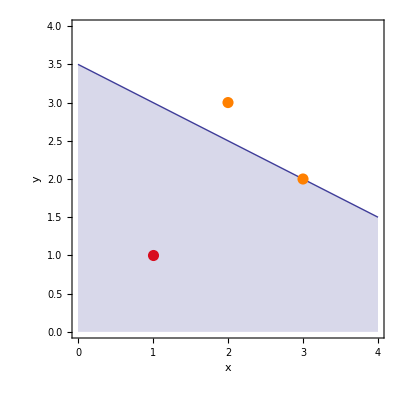

```mathematica
points0=ListPlot[{x01,x11[a,b]},PlotStyle->{Thick,PointSize[0.02],Orange},PlotRange-> {0,4}];
points1=ListPlot[{x02},PlotStyle->{Thick,PointSize[0.02],Red},PlotRange-> {0,4}];
nodesPlot=Plot[nodes,{c,0,4},Filling-> Axis,PlotStyle-> Thick,AxesOrigin-> {0,0},PlotRange-> {{0,4}{0,4}}];
Show[points1,nodesPlot,points0,Frame->True,AspectRatio-> 1,FrameLabel-> {Style["x",Bold],Style["y",Bold]},LabelStyle->Directive[FontFamily->"Helvetica"],RotateLabel-> False,AxesOrigin-> {0,0}]
```